#### Лабораторная работа 2 Численное решение нелинейных уравнений Вариант 8

Задание 1. Отделите графически корни алгебраического уравнения f(x) = 0 с помощью функции Plot. Найдите один из них (нецелый) с точностью ϵ = 10^-3 методом хорд. Укажите потребовавшееся число итераций. Проиллюстрируйте графически нахождение первых двух приближений (постройте график функции и хорды).

```mathematica
f[x_]=12 x^3+29 x^2-52x+11;
```

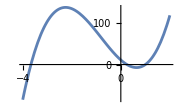

```mathematica
Plot[f[x], {x,-4, 2}, AxesOrigin-> {0,0},ImageSize->Small]
```

По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах (-4, - 3), (0, 0.5) и (0.5, 1.5).

```mathematica
f[x_]=12 x^3+29 x^2-52x+11;
```

```mathematica
a=-4;
b=-3;
```

В соответствии с методом хорд, организуем цикл с помощью оператора While.

```mathematica
eps=0.001;
ex=eps*10;
If[f[a]*f''[a]>0,xn0=b;g[x_]:=a-(f[a]*(x-a)/(f[x]-f[a]));
hord[x_,xn_]:=f[xn]+((x-xn)/(xn-a)*(f[xn]-f[a])),xn0=a;g[x_]:=x-(f[x]*(b-x)/(f[b]-f[x]));
hord[x_,xn_]:=f[xn]+((x-xn)/(xn-b)*(f[xn]-f[b]))];
```

```mathematica
xn1=g[xn0];n=1;

While[ex>eps,If[n==2,Print[Plot[{f[x],hord[x,xn1],hord[x,xn0],hord[x,xn01]},{x,a,b},Epilog->{Green,Dashed,InfiniteLine[{xn1,0},{0,1}],InfiniteLine[{xn0,0},{0,1}],PointSize[0.013],Point[{{xn0,0},{xn0,f[xn0]},{xn1,0},{xn1,f[xn1]},{g[xn1],0}}]},PlotRange->40]]];
```

```mathematica
xn01=xn0;xn0=xn1;
xn1=g[xn0];
ex=((xn1-xn0)^2)/(Abs[xn1+xn01-2 xn0])
```

```mathematica
n=n+1;]
Print["Решение х= ",xn1//N," Шаг= ",n]
```

Результат работы метода хорд.

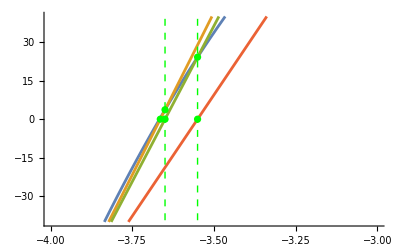

Решение х= -3.66633 Шаг= 4

Задание 2. Отделите графически и найдите с помощью функций Solve, NSolve, Roots, FindRoot корни алгебраического уравнения f(x) = 0. Разложите многочлен f(x) на множители, используя функцию Factor.

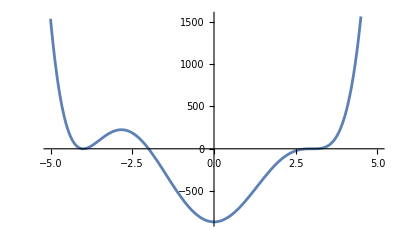

```mathematica
f1[x_]= x^6 + x^5-31 x^4-13 x^3+306 x^2-864;
Plot[{f1[x]}, {x, -5, 5}, AxesOrigin-> {0,0}]
```

По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах (-4.5, - 3.5), (-2.5, -1.5) и (2.5, 3.5).

```mathematica
Solve[f1[x]== 0 ]
```

{{x→-4},{x→-4},{x→-2},{x→3},{x→3},{x→3}}

```mathematica
NSolve[f1[x]==0]
```

{{x→-4.},{x→-4.},{x→-2.},{x→3.},{x→3.},{x→3.}}

```mathematica
Roots[f1[x] == 0, x]
```

x==-4||x==-4||x==-2||x==3||x==3||x==3

```mathematica
Factor[f1[x]]
```

(-3+x)^3 (2+x) (4+x)^2

Как видно, данное уравнение имеет три корня, причем корни −4 и 3 являются двукратным и трёхкратным корнями соответственно.

```mathematica
FindRoot[f1[x]== 0, {x, -5}]
```

{x→-4.}

```mathematica
FindRoot[f1[x]== 0, {x, -1}]
```

{x→-2.}

```mathematica
FindRoot[f1[x]== 0, {x, 2}]
```

{x→2.99999}

Задание 3. Отделите графически корни трансцендентного уравнения с помощью функции Plot. Найдите один из них с точностью ϵ  = 10^-3: 
а) методом Ньютона; 
б) методом секущих. 
Укажите потребовавшееся число итераций.

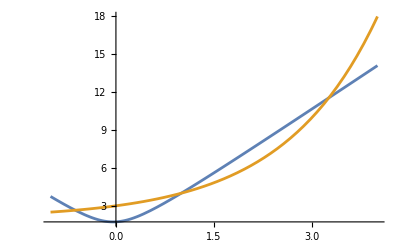

```mathematica
f2[x_] = √(12 x^2+x+3);
g2[x_] = 2^x+2;
Plot[{f2[x],g2[x]},{x,-1,4}]
```

Уравнение имеет три корня. Они расположены в интервалах 
(-1, 0), (0.5, 1.5) и (3, 4).

а) Метод Ньютона:

```mathematica
f3[x_] =√(12 x^2+x+3) -  2^x+2; 
a = 3; b=4; e = 0.001;
x1 = b;
Do[x2= x1;
x1 = (x1-f3[x1]/f3'[x1])//N;
```

```mathematica
If[Abs[x2-x1]< e,
Print["Решение x = ",x2//N, " получено на ",n, " шаге."];
Break[]],
{n,1,100}]
```

Решение x = 4.01395 получено на 2 шаге.

б) Метод секущих:

```mathematica
f3[x_] =√(12 x^2+x+3) -  2^x+2; 
c = 3; d=4; e = 0.001;
x1 = c;
x2 = d;
Do[x3= x2;
x2 = x2 - (x2-x1)/(f3[x2] - f3[x1])* f3[x2]//N;
```

```mathematica
If[Abs[x3-x2]< e,
Print["Решение x = ",x3//N, " получено на ",n, " шаге."];
Break[]],
{n,1,100}]
```

Решение x = 4.0143 получено на 10 шаге.

Задание 4. Приведите уравнение 3.8 к виду, пригодному для итераций. Найдите его корни методом простых итераций с точностью ϵ  = 10^-3. Укажите потребовавшееся число итераций.

```mathematica
f4[x_] =√(12 x^2+x+3) -  2^x+2; 
Plot[{f4[x]}, {x, 0, 5}, AxesOrigin-> {0,0}]
```

```mathematica
g[x_] :=f4'[x];
a= 3.5;
b=4.5;
```

```mathematica
If[Abs[g[a]]>Abs[g[b]],eps = g[a], eps=g[b]];
p[x_]:=x-(2/eps)*f4[x];
e=0.001;
i=0;
```

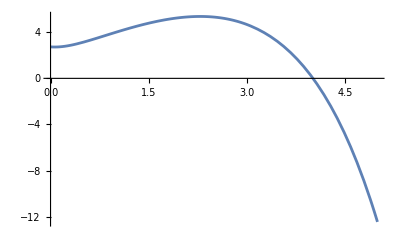

Решение x = 4.014 получено на 6 шаге.

```mathematica
While[Abs[a-b]>e,
Increment[i];
a=b;
b=p[a];
];
Print["Решение x = ", b//N, " получено на ", i, " шаге."];
```

Задание 5.  Решите уравнение (3.1 – 3.16) с помощью функций Solve, NSolve, FindRoot.

```mathematica
f5[x_] = √(12 x^2+x+3);
g5[x_] = 2^x+2;
Solve[f5[x]==g5[x]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[√(3+x+12 x^2)==2+2^x]

```mathematica
NSolve[f5[x]==g5[x]]
```

{{x→1.},{x→3.25594},{x→5.34642+10.7214 ⅈ},{x→6.16909+19.9993 ⅈ},{x→6.68966+29.1602 ⅈ},{x→7.07166+38.2811 ⅈ},{x→7.37357+47.383 ⅈ},{x→7.62323+56.4744 ⅈ},{x→7.83606+65.5592 ⅈ},{x→8.02154+74.6397 ⅈ},{x→8.18591+83.7172 ⅈ},{x→8.33347+92.7924 ⅈ},{x→8.46735+101.866 ⅈ},{x→8.58987+110.938 ⅈ},{x→8.70281+120.01 ⅈ},{x→8.80755+129.08 ⅈ}}

```mathematica
FindRoot[f5[x]==g5[x], {x, -1}]
```

{x→-0.622041}

```mathematica
FindRoot[f5[x]==g5[x], {x, 1}]
```

{x→1.}

```mathematica
FindRoot[f5[x]==g5[x], {x, 3}]
```

{x→3.25594}

Задание 6. Дана система двух нелинейных уравнений f(x, y) = 0, g(x, y) = 0. Используя средства пакета Mathematica, изобразите на одном чертеже кривые f (x, y) = 0 и g(x, y) = 0, и решите данную систему.

```mathematica
g1[x_,y_]=Sinh[2y-x]-3x+1-y;
g2[x_,y_]= 32(y^2-x^2)-(y^2+x^2)^2;
```

```mathematica
gr1= ContourPlot[g1[x,y]==0, {x,-5,5},{y,-6,6}, Axes->True, Frame->False,ImageSize->Small]
```

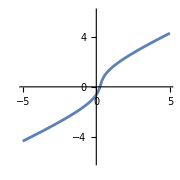

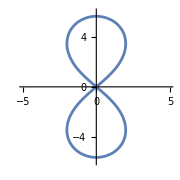

```mathematica
gr2 = ContourPlot[g2[x,y]==0, {x,-5,5},{y,-6,6}, Axes->True, Frame->False,ImageSize->Small]
```

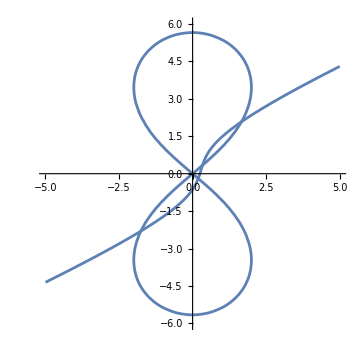

```mathematica
Show[gr1, gr2, ImageSize->Medium]
```

По графику видно, что кривые пересекаются в четырёх точках. Они расположены вблизи точек (-2, - 2), (0.5, -0.5), (0.5, 0.5) и (2, 2). Эти точки и будем использовать как начальные приближения.

```mathematica
FindRoot[{g1[x,y]==0, g2[x,y]==0},{x,-2},{y,-2}]
```

{x→-1.76022,y→-2.30332}

```mathematica
FindRoot[{g1[x,y]==0, g2[x,y]==0},{x,0.5},{y,-0.5}]
```

{x→0.193271,y→-0.193723}

```mathematica
FindRoot[{g1[x,y]==0, g2[x,y]==0},{x,0.5},{y,0.5}]
```

{x→0.336354,y→0.338757}

```mathematica
FindRoot[{g1[x,y]==0, g2[x,y]==0},{x,2},{y,2}]
```

{x→1.66188,y→2.08239}